### Trigonometric properties

```mathematica
I4=IdentityMatrix[4];
beta={β[t]->ArcTan[L,lr*Tan[δ[t]]]};
betaInv={ArcTan[L,lr*Tan[δ[t]]]->β[t]};
betaR={β->ArcTan[L,lr*Tan[δ]]};
betaInvR={ArcTan[L,lr*Tan[δ]]->β};
sinB={Tan[δ[t]]/(√(L^2+lr^2 Tan[δ[t]]^2))->Sin[β[t]]/lr};
sinBR={Tan[δ]/(√(L^2+lr^2 Tan[δ]^2))->Sin[β]/lr};
reduce={(L^2+lr^2 Tan[δ[t]]^2)->L^2/Cos[β[t]]^2};
reduceR={(L^2+lr^2 Tan[δ]^2)->L^2/Cos[β]^2};
```

### Nonlinear model

```mathematica
MatrixForm[f = {
v[t]*Cos[θ[t]+β[t]],
v[t]*Sin[θ[t]+β[t]],
D[v[t],t],
v[t]*Cos[β[t]]*Tan[δ[t]]/L
}/.beta]/.betaInv
```

(Cos[β[t]+θ[t]] v[t]
Sin[β[t]+θ[t]] v[t]
v'[t]
(Tan[δ[t]] v[t])/(√(L^2+lr^2 Tan[δ[t]]^2)))

### Linearization

```mathematica
MatrixForm[A[t]=D[f,{{x[t],y[t],v[t],θ[t]}}]]/.betaInv/.sinB
```

(0 | 0 | Cos[β[t]+θ[t]] | -Sin[β[t]+θ[t]] v[t]
0 | 0 | Sin[β[t]+θ[t]] | Cos[β[t]+θ[t]] v[t]
0 | 0 | 0 | 0
0 | 0 | Sin[β[t]]/lr | 0)

```mathematica
MatrixForm[FullSimplify[FullSimplify[(D[f,{{D[v[t],t],δ[t]}}])]/.reduce/.betaInv, Sec[β[t]]>0&&L>0]]
MatrixForm[B[t]=FullSimplify[D[f,{{D[v[t],t],δ[t]}}]]];
```

(0 | -(lr Cos[β[t]]^2 Sec[δ[t]]^2 Sin[β[t]+θ[t]] v[t])/L
0 | (lr Cos[β[t]]^2 Cos[β[t]+θ[t]] Sec[δ[t]]^2 v[t])/L
1 | 0
0 | (Cos[β[t]]^3 Sec[δ[t]]^2 v[t])/L)

The denominator of B has 2 solutions -Sec[B[t]]^3, and Sec[B[t]]^3, since B[t]∈[-π/2,π/2]  then  Sec[B[t]]>0. Since I used +Cos to build the Cos^2 that became Sec^2, then taking sqrt should use the same +Cos used to build it

### Discretization

```mathematica
approxConst={δ[t]->δ,β[t]->β,θ[t]->θ,v[t]->v};
```

#### Euler

```mathematica
MatrixForm[I4+A[t]*T]/.betaInv /.sinB/.approxConst
MatrixForm[FullSimplify[B[t]*T/.reduce/.betaInv,Sec[β[t]]>0&&L>0]]/.approxConst
```

(1 | 0 | T Cos[β+θ] | -T v Sin[β+θ]
0 | 1 | T Sin[β+θ] | T v Cos[β+θ]
0 | 0 | 1 | 0
0 | 0 | (T Sin[β])/lr | 1)

(0 | -(lr T v Cos[β]^2 Sec[δ]^2 Sin[β+θ])/L
0 | (lr T v Cos[β]^2 Cos[β+θ] Sec[δ]^2)/L
T | 0
0 | (T v Cos[β]^3 Sec[δ]^2)/L)

#### Exact discretization

```mathematica
MatrixForm[Ad=MatrixExp[Integrate[A[t]/.approxConst,{t,k*T,(k+1)*T}]]//FullSimplify]/.betaInvR/.sinBR
```

(1 | 0 | T Cos[β+θ]-(T^2 v Sin[β] Sin[β+θ])/(2 lr) | -T v Sin[β+θ]
0 | 1 | (T^2 v Cos[β+θ] Sin[β])/(2 lr)+T Sin[β+θ] | T v Cos[β+θ]
0 | 0 | 1 | 0
0 | 0 | (T Sin[β])/lr | 1)

```mathematica
MatrixForm[Ared=A[t]/.approxConst/.betaInvR/.sinBR/.reduceR];
MatrixForm[Bred=FullSimplify[B[t]/.approxConst/.betaInvR/.sinBR/.reduceR,Sec[β]>0&&L>0]];
MatrixForm[Bd=FullSimplify[((T*I4+A[t]*T^2/2+A[t].A[t]*T^3/6).(B[t]))/.approxConst]];
MatrixForm[(T*I4+Ared*T^2/2+Ared.Ared*T^3/6).(Bred)]
```

(1/2 T^2 Cos[β+θ]-(T^3 v Sin[β] Sin[β+θ])/(6 lr) | -(lr T v Cos[β]^2 Sec[δ]^2 Sin[β+θ])/L-(T^2 v^2 Cos[β]^3 Sec[δ]^2 Sin[β+θ])/(2 L)
(T^3 v Cos[β+θ] Sin[β])/(6 lr)+1/2 T^2 Sin[β+θ] | (lr T v Cos[β]^2 Cos[β+θ] Sec[δ]^2)/L+(T^2 v^2 Cos[β]^3 Cos[β+θ] Sec[δ]^2)/(2 L)
T | 0
(T^2 Sin[β])/(2 lr) | (T v Cos[β]^3 Sec[δ]^2)/L)

#### With pseudoinverse (wrong)

```mathematica
MatrixForm[Ainv=FullSimplify[PseudoInverse[A[t]/.approxConst],{δ,L,lr,v,β,θ,1/(√(L^2+lr^2 Tan[δ]^2))}∈Reals]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
(2 Cos[δ] (L Cos[δ] Cos[θ]-lr Sin[δ] Sin[θ]) √(L^2+lr^2 Tan[δ]^2))/(1+L^2+lr^2+(-1+L^2-lr^2) Cos[2 δ]) | (2 Cos[δ] (lr Cos[θ] Sin[δ]+L Cos[δ] Sin[θ]) √(L^2+lr^2 Tan[δ]^2))/(1+L^2+lr^2+(-1+L^2-lr^2) Cos[2 δ]) | 0 | (Sin[2 δ] √(L^2+lr^2 Tan[δ]^2))/(1+L^2+lr^2+(-1+L^2-lr^2) Cos[2 δ])
-Sin[θ+ArcTan[L,lr Tan[δ]]]/v | Cos[θ+ArcTan[L,lr Tan[δ]]]/v | 0 | 0)

```mathematica
MatrixForm[FullSimplify[FullSimplify[Ainv.(Ad-I4).(B[t]/.approxConst)]/.sinBR/.reduceR, L>0&&Sec[β]>0]]
```

(0 | 0
0 | 0
T | 0
(T^2 Sin[β])/(2 lr) | (T v Cos[β]^3 Sec[δ]^2)/L)

### Simulate linearization

```mathematica
Integrate[Exp[a*t],t]
```

ⅇ^(a t)/a

```mathematica
Solve[a*x+b*u+c==x,u]
```

{{u→(-c+x-a x)/b}}

```mathematica
Solve[Ad.{{x0},{x1},{x2},{x3}}+Bd.{{u0},{u1}}+{{c1},{c2},{c3},{c4}}=={{x0},{x1},{x2},{x3}},{u0,u1}]
```

{}

```mathematica
Simplify[Ad/.{v->0,θ->0,δ->0},L>0]//MatrixForm
Simplify[Bd/.{v->0,θ->0,δ->0},L>0]//MatrixForm
```

(1 | 0 | T | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(T^2/2 | 0
0 | 0
T | 0
0 | 0)

```mathematica
Simplify[Ad/.{θ->0,δ->0},L>0]//MatrixForm
Simplify[Bd/.{θ->0,δ->0},L>0]//MatrixForm
```

(1 | 0 | T | 0
0 | 1 | 0 | T v
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(T^2/2 | 0
0 | (T v (2 lr+T v))/(2 L)
T | 0
0 | (T v)/L)

```mathematica
Simplify[Ad/.{δ->0},L>0]//MatrixForm
Simplify[Bd/.{δ->0},L>0]//MatrixForm
```

(1 | 0 | T Cos[θ] | -T v Sin[θ]
0 | 1 | T Sin[θ] | T v Cos[θ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1/2 T^2 Cos[θ] | -(T v (2 lr+T v) Sin[θ])/(2 L)
1/2 T^2 Sin[θ] | (T v (2 lr+T v) Cos[θ])/(2 L)
T | 0
0 | (T v)/L)

```mathematica
f//MatrixForm
```

(Cos[ArcTan[L,lr Tan[δ[t]]]+θ[t]] v[t]
Sin[ArcTan[L,lr Tan[δ[t]]]+θ[t]] v[t]
v'[t]
(Tan[δ[t]] v[t])/(√(L^2+lr^2 Tan[δ[t]]^2)))

```mathematica
k1=T*f;
k1cond={x[t]->x[t]+k1[[1]]/2,y[t]->y[t]+k1[[2]]/2,v[t]->v[t]+k1[[3]]/2,θ[t]->θ[t]+k1[[4]]/2};
k2=T*f/.k1cond;
k2cond={x[t]->x[t]+k2[[1]]/2,y[t]->y[t]+k2[[2]]/2,v[t]->v[t]+k2[[3]]/2,θ[t]->θ[t]+k2[[4]]/2};
k3=T*f/.k2cond;
k3cond={x[t]->x[t]+k3[[1]],y[t]->y[t]+k3[[2]],v[t]->v[t]+k3[[3]],θ[t]->θ[t]+k3[[4]]};
k4=T*f/.k3cond;
rk4={x[t],y[t],v[t],θ[t]}+(k1+2*k2+2*k3+k4)/6;
rk4/.approxConst/.betaInvR/.sinBR/.reduceR//MatrixForm
Simplify[rk4/.approxConst/.betaInvR/.sinBR/.reduceR/.{β->0}]//Simplify//MatrixForm
```

(x[t]+1/6 (T v Cos[β+θ]+2 T Cos[β+θ+(T v Sin[β])/(2 lr)] (v+1/2 T v'[t])+2 T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)] (v+1/2 T v'[t])+T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr] (v+T v'[t]))
y[t]+1/6 (T v Sin[β+θ]+2 T Sin[β+θ+(T v Sin[β])/(2 lr)] (v+1/2 T v'[t])+2 T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)] (v+1/2 T v'[t])+T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr] (v+T v'[t]))
v+T v'[t]
θ+1/6 ((T v Sin[β])/lr+(4 T Sin[β] (v+1/2 T v'[t]))/lr+(T Sin[β] (v+T v'[t]))/lr))

(x[t]+1/2 T Cos[θ] (2 v+T v'[t])
y[t]+1/2 T Sin[θ] (2 v+T v'[t])
v+T v'[t]
θ)

```mathematica
rk4
```

{x[t]+1/6 (T Cos[ArcTan[L,lr Tan[δ[t]]]+θ[t]] v[t]+2 T Cos[ArcTan[L,lr Tan[δ[t]]]+(T Tan[δ[t]] v[t])/(2 √(L^2+lr^2 Tan[δ[t]]^2))+θ[t]] (v[t]+1/2 T v'[t])+2 T Cos[ArcTan[L,lr Tan[δ[t]]]+θ[t]+(T Tan[δ[t]] (v[t]+1/2 T v'[t]))/(2 √(L^2+lr^2 Tan[δ[t]]^2))] (v[t]+1/2 T v'[t])+T Cos[ArcTan[L,lr Tan[δ[t]]]+θ[t]+(T Tan[δ[t]] (v[t]+1/2 T v'[t]))/(√(L^2+lr^2 Tan[δ[t]]^2))] (v[t]+T v'[t])),y[t]+1/6 (T Sin[ArcTan[L,lr Tan[δ[t]]]+θ[t]] v[t]+2 T Sin[ArcTan[L,lr Tan[δ[t]]]+(T Tan[δ[t]] v[t])/(2 √(L^2+lr^2 Tan[δ[t]]^2))+θ[t]] (v[t]+1/2 T v'[t])+2 T Sin[ArcTan[L,lr Tan[δ[t]]]+θ[t]+(T Tan[δ[t]] (v[t]+1/2 T v'[t]))/(2 √(L^2+lr^2 Tan[δ[t]]^2))] (v[t]+1/2 T v'[t])+T Sin[ArcTan[L,lr Tan[δ[t]]]+θ[t]+(T Tan[δ[t]] (v[t]+1/2 T v'[t]))/(√(L^2+lr^2 Tan[δ[t]]^2))] (v[t]+T v'[t])),v[t]+T v'[t],θ[t]+1/6 ((T Tan[δ[t]] v[t])/(√(L^2+lr^2 Tan[δ[t]]^2))+(4 T Tan[δ[t]] (v[t]+1/2 T v'[t]))/(√(L^2+lr^2 Tan[δ[t]]^2))+(T Tan[δ[t]] (v[t]+T v'[t]))/(√(L^2+lr^2 Tan[δ[t]]^2)))}

```mathematica
Simplify[(D[rk4,{{x[t],y[t],v[t],θ[t]}}])/.approxConst/.betaInvR/.sinBR/.reduceR]//MatrixForm
```

(1 | 0 | 1/6 (T Cos[β+θ]+2 T Cos[β+θ+(T v Sin[β])/(2 lr)]+2 T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)]+T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr]-(T^2 Sin[β] Sin[β+θ+(T v Tan[δ])/(2 √(L^2 Sec[β]^2))] (v+1/2 T v'[t]))/lr-(T^2 Sin[β] Sin[β+θ+(T Tan[δ] (v+1/2 T v'[t]))/(2 √(L^2 Sec[β]^2))] (v+1/2 T v'[t]))/lr-(T^2 Sin[β] Sin[β+θ+(T Tan[δ] (v+1/2 T v'[t]))/(√(L^2 Sec[β]^2))] (v+T v'[t]))/lr) | 1/6 (-T v Sin[β+θ]-2 T Sin[β+θ+(T v Sin[β])/(2 lr)] (v+1/2 T v'[t])-2 T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)] (v+1/2 T v'[t])-T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr] (v+T v'[t]))
0 | 1 | 1/6 (T Sin[β+θ]+2 T Sin[β+θ+(T v Sin[β])/(2 lr)]+2 T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)]+T Sin[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr]+(T^2 Cos[β+θ+(T v Tan[δ])/(2 √(L^2 Sec[β]^2))] Sin[β] (v+1/2 T v'[t]))/lr+(T^2 Cos[β+θ+(T Tan[δ] (v+1/2 T v'[t]))/(2 √(L^2 Sec[β]^2))] Sin[β] (v+1/2 T v'[t]))/lr+(T^2 Cos[β+θ+(T Tan[δ] (v+1/2 T v'[t]))/(√(L^2 Sec[β]^2))] Sin[β] (v+T v'[t]))/lr) | 1/6 (T v Cos[β+θ]+2 T Cos[β+θ+(T v Sin[β])/(2 lr)] (v+1/2 T v'[t])+2 T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/(2 lr)] (v+1/2 T v'[t])+T Cos[β+θ+(T Sin[β] (v+1/2 T v'[t]))/lr] (v+T v'[t]))
0 | 0 | 1 | 0
0 | 0 | (T Sin[β])/lr | 1)

### Tests

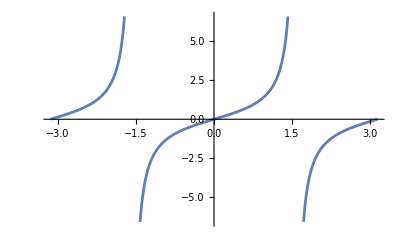

```mathematica
Plot[Tan[angle],{angle,-π,π}]
```

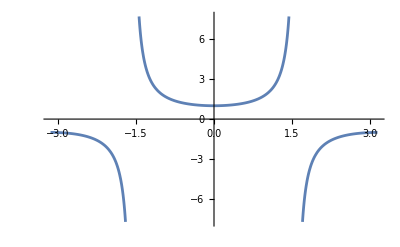

```mathematica
Plot[Sec[angle],{angle,-π,π}]
```

```mathematica
FullSimplify[(Sec[angle]^2)^(3/2),angle∈Reals]
```

Abs[Sec[angle]]^3

```mathematica
FullSimplify[(a^2)^(3/2),a∈Reals]
```

Abs[a]^3

```mathematica
Solve[d^2==(Sec[β]^2)^3,d]
```

{{d→-Sec[β]^3},{d→Sec[β]^3}}

```mathematica
FullSimplify[(a^2)^(3/2)]
```

(a^2)^(3/2)

```mathematica
((-1)^2)^(3/2)
```

1

```mathematica
(-1)^3
```

-1

```mathematica
FullSimplify[((1/Sec[angle])^2)^(3/2),angle∈Reals]
```

Abs[Cos[angle]]^3

```mathematica
((-1)^(3/2))^2
```

-1

```mathematica
((-1)^2)^(3/2)
```

1

```mathematica
FullSimplify[((a)^(3/2))^2,a∈Reals]
FullSimplify[((a)^2)^(3/2),a∈Reals]
```

a^3

Abs[a]^3

```mathematica
FullSimplify[((-1)^(3/2))^2]
```

-1

```mathematica
FullSimplify[(1)^(1/2)]
```

1

```mathematica
FullSimplify[((a)^(3/2))^2,a<1]
FullSimplify[((a)^2)^(3/2),a<1]
```

a^3

Abs[a]^3

```mathematica
FullSimplify[(2^2)^(3/2)]
```

8

```mathematica
FullSimplify[3^(1/2)]
```

√3

```mathematica
β[t]∈Reals&&L>0
```

β[t]∈ℝ&&L>0

### Tests2

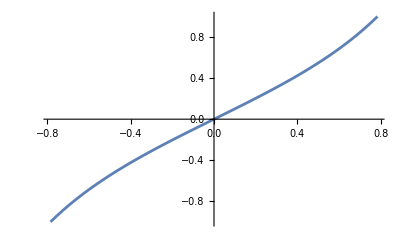

```mathematica
Plot[Tan[δ],{δ,-π/4,π/4}]
```

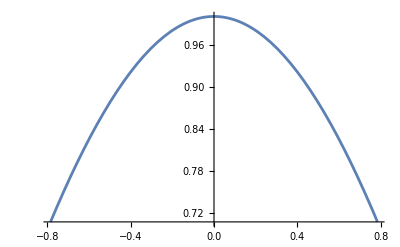

```mathematica
Plot[Cos[δ],{δ,-π/4,π/4}]
```

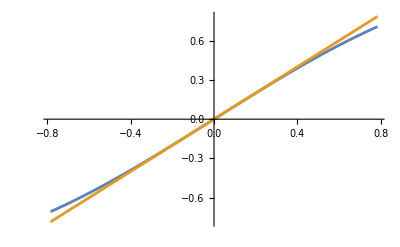

```mathematica
Plot[{Sin[δ],δ},{δ,-π/4,π/4}]
```

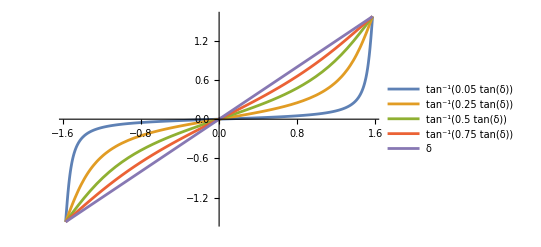

```mathematica
Plot[{ArcTan[0.05*Tan[δ]],ArcTan[0.25*Tan[δ]],ArcTan[0.5*Tan[δ]],ArcTan[0.75*Tan[δ]],δ},{δ,-π/2,π/2},
PlotLegends->"Expressions"]
```

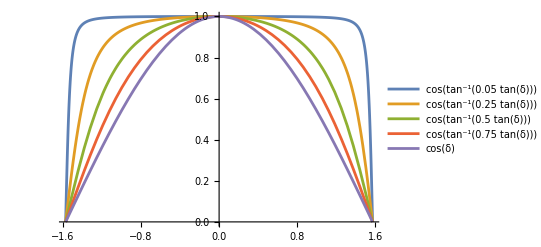

```mathematica
Plot[{Cos[ArcTan[0.05*Tan[δ]]],Cos[ArcTan[0.25*Tan[δ]]],Cos[ArcTan[0.5*Tan[δ]]],Cos[ArcTan[0.75*Tan[δ]]],Cos[δ]},{δ,-π/2,π/2},
PlotLegends->"Expressions"]
```